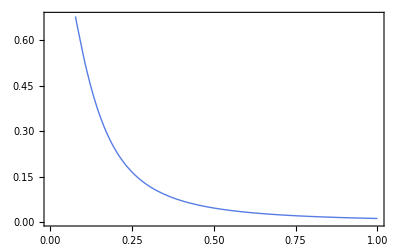

```mathematica
L = 20/4999;
ω = 0.0002;
m = 10000;
p = 10;
X = 2;
(*Eo = p^2/(2m)+0.5m ω^2X^2;*)
Eo = ∫_(-∞)^∞ 1/(2π)^(1/2)(D[Exp[-(x+X)^2/4],x]D[ Exp[-(x+X)^2/4],x]/(2m)+0.5m ω^2Exp[-(x+X)^2/4]x^2Exp[-(x+X)^2/4])ⅆx; 
β[U_] = Sqrt[2m(U-Eo)];
γ[U_] = 0.25((1-Eo/U)/(Eo/U)-2+(Eo/U)/(1-Eo/U));
T[U_]=1/(Cosh[β[U] L]^2 + γ[U] Sinh[β[U] L]^2);
Plot[Evaluate[T[U]],{U,0.001,1},PlotStyle->Thick,PlotTheme->{"BoldColors","Frame"},FrameStyle->Directive[14,Black]]
```

```mathematica
(*∫_(-∞)^∞ 1/(2π)^(1/2)(D[Exp[-(x-X)^2/4],x]D[ Exp[-(x-X)^2/4],x]/(2m)+0.5m ω^2Exp[-(x-X)^2/4]x^2Exp[-(x-X)^2/4])ⅆx
p^2/(2m)+0.5m ω^2X^2*)
```

```mathematica
T[0.1118]
```

0.500069

```mathematica
0.1118m/(p)
```

111.8

```mathematica
(*a=200;
b=10.;
sol=NDSolve[{I D[u[t,x],t]==(-1/2) D[u[t,x],{x,2}]+0.15 UnitStep[x] u[t,x],u[0.,x]==Exp[-((x+0.7*a)^2./(2*b^2))] Exp[I x/2.],u[t,a]==0,u[t,-a]==0},u,{t,0,4000},{x,-a,a},AccuracyGoal->4,PrecisionGoal->8]

Animate[Plot[Evaluate[Abs[u[t,x]]^2/. First[sol]],{x,-a,a},PlotRange->{0,1}],{t,0,750,0.005}]*)
```

```mathematica
(*ψl = 1/(2π)^(1/4)Exp[-(x-s)^2/4+I p x] + 1/(2π)^(1/4)Exp[-(x-s)^2/4-I p x] ;
eq1=-0.7*w+0.3*y+0.4*z==0;
eq2=-0.6*x+0.2*y+0.1*z==0;
eq3=0.5*w+0.3*x-y==0;
eq4=0.2*w+0.3*x+0.5*y-0.5*z==0;
eq5=w+x+y+z==1;
Solve[{eq1,eq2,eq3,eq4,eq5},{z,w,x,y}]*)
```